# Mars 2020 EDL Image Processing

## Descent Stage Down-Look Camera

Mars 2020 had 7 cameras for entry, descent, and landing (EDL). The Descent stage Downlook Camera was in the unique position to record images of the Mastcam-Z Radiometric Calibration Targets. This notebook contains transforms to “develop” raw image data into plausible-color images.

The transforms are produced by optimizing model parameters that transform samples of raw data to match corresponding colors on the primary Mastcam-Z Radiometric Calibration Target.

The principal model  (modelW10) consists of  an Input Device Transform (IDT) matrix that maps raw RGB to CIEXYZ values, and a black-body radiator spectral power distribution (SPD) illuminating  the calibration target.

The secondary model  (modelW11) consists of an IDT, with the CIE D65 standard illuminant SPD illuminating  the calibration target.

Model parameters are fit by minimizing CIE2000 color distance between IDT transformed raw colors and calibration target colors produced from the illuminant SPD and calibration target reflectance data. 

Process using modelW10,

convert raw data to XYZ using IDT

chromatic adaption from the model black-body illuminant to D65

convert to “okLab” color space for saturation reduction in ares where raw data clipping. Clipping occurs in raw data due to over exposure of bright areas and camera recording format being 8-bit linear.

convert from “okLab” back to XYZ and then to sRGB

Processing using modelW11 is similar, however it does not include  chromatic adaption step.

### The Camera

The DDC camera detector model is Sony IMX265.

The actual camera model may be FLIR Chameleon3  CM3-U3-31S4C-CS   https://www.flir.com/products/chameleon3-usb3/?model=CM3-U3-31S4C-CS

Notes from “TECHNICAL REFERENCE for FLIR CHAMELEON®3”:
	8.4.5.2 For Resolution 2048 x 1536 Mode 0 RAW8 mode 55FPS, RAW16 31FPS, doesn’t show RAW12 option
	8.13 Gama not available in RAW mode, doesn’t explicitly say LUT is not available
	1.6 Least significant bits dropped

Figure 9 in (Maki et al 2020) shows frame rate of 12fps. In 8-bit 2048 x 1536 resolution raw mode, camera should have been able to operate at 55fps, so I assume lower rate due to data-handling/communication system rate limitations.

### The Calibration Target

Reflectance measurements from (Buz el al. 2020) data are used to derive the targets colors from illumination SPDs. The Buz measurements are from “witness samples”. Per (Kinch et al. 2020) “Spectra from witness samples match spectra from the center of color and grayscale patches and match spectra acquired on grayscale rings well...”.

From “Page 7 of 51” of (Kinch et al. 2020):
The white ring and white patch are made from AluWhite98 sintered alumina provided by Avian technologies in the US (www.aviantechnologies.com). The rest (all colors, blacks, and greys) are made from glazed and matted aluminum-silicates provided by Lucideon in the UK (www.lucideon.com). The names of the 7 materials provided by Lucideon are Black, Grey33, Grey70, Cyan, Green, Bright Yellow and Red.

Prior to using the Buz spectra, reflectance of of grey targets was estimated as  (1, .75, .4, .1) from (Kinch et al. 2020) Page 12/51 Fig 6. From Table 2 reflectance of of grey targets in visible light region was estimated as (1.01, .79, .43, .1)

## References/Information Sources

Mars “RAW” images
https://mars.nasa.gov/mars2020/multimedia/raw-images/

“The Mars 2020 Engineering Cameras and Microphone on the Perseverance Rover: A Next-Generation Imaging System for Mars Exploration” https://doi.org/10.1007/s11214-020-00765-9

“Photometric characterization of Lucideon and Avian Technologies color standards including application for calibration of the Mastcam-Z instrument on the Mars 2020 rover” https://doi.org/10.1117/1.OE.58.2.027108

“Dataset accompanying “Photometric characterization of Lucideon and Avian Technologies color standards including application for calibration of the Mastcam-Z instrument on the Mars 2020 rover” https://doi.org/10.22002/D1.1154

“Radiometric Calibration Targets for the Mastcam-Z Camera on the Mars 2020 Rover Mission” https://doi.org/10.1007/s11214-020-00774-8 https://link.springer.com/content/pdf/10.1007/s11214-020-00774-8.pdf

“Perseverance Rover’s Descent and Touchdown on Mars: Onboard Camera Views” JPL 4K EDL Video 
https://mars.nasa.gov/resources/25628/perseverance-rovers-descent-and-touchdown-on-mars-onboard-camera-views/

“TECHNICAL REFERENCE for FLIR CHAMELEON®3” https://flir.boxcn.net/s/xobncd08w5w3oc72tmvs33dnttqfpjw9

“IMAGING PERFORMANCE SPECIFICATION FLIRCHAMELEON®3” https://flir.boxcn.net/s/62dooxqcmu4chhxweyvp5wf9kocnliwr

“FLIR Machine Vision Cameras are Headed to Mars!” Blog entry https://www.flir.com/discover/iis/flir-machine-vision-cameras-are-headed-to-mars/
“FLIR Machine Vision Cameras Capture High-Definition Footage of NASA’s Perseverance Rover Landing on Mars” Blog Entry https://www.flir.com/discover/iis/flir-machine-vision-cameras-capture-high-definition-footage-of-nasas-perseverance-rover-landing-on-mars/

“NOIP1SN1300A PYTHON 1.3/0.5/0.3 MegaPixels Global Shutter CMOS
Image Sensors” On Semi P1300 data-sheet for other EDL cameras
https://www.onsemi.com/pdf/datasheet/noip1sn1300a-d.pdf
(Response curve looks a lot like that for IMX264 sensor)

“FSM-IMX264 Datasheet” includes response curve for IMX264. Not sure how close this is to IMX265  https://www.framos.com/media/pdf/46/11/8e/FSM-IMX264_Datasheet_v1-0g_BriefsQt12dxNWYGtz.pdf

“The Cameras on the Mars 2020 Perseverance Rover” https://mars.nasa.gov/mars2020/spacecraft/rover/cameras/
Mentions only 2 of 3 Parachute “up look” cameras successfully recorded the parachute.

ACES - DRAFT P-2013-001 : Recommended Procedures for the Creation and Use of Digital Camera System Input Device Transforms (IDTs) http://j.mp/P-2013-001 https://www.oscars.org/science-technology/aces/aces-documentation

Press Release: Avian Technologies Standards Land on Mars https://aviantechnologies.com/2021/02/21/press-release-avian-technologies-standards-land-on-mars/

### Additional Information

Early Navcam image of calibration target: “Mars Perseverance Sol 9: Left Navigation Camera (Navcam)”   https://mars.nasa.gov/mars2020/multimedia/raw-images/NLE_0009_0667755636_926ECM_N0030000NCAM05000_13_0LLJ

“Mars 2020 Perseverance SHERLOC WATSON Camera Pre-delivery Characterization and Calibration Report” 
https://www.researchgate.net/publication/345959204_Mars_2020_Perseverance_SHERLOC_WATSON_Camera_Pre-delivery_Characterization_and_Calibration_Report/link/5fb30ee945851518fdaca577/download

“Orientation to Perseverance’s Raw Image Data and Metadata” Emily Lakdawalla  https://www.patreon.com/posts/orientation-to-48263650

“Decoding the Raw Publicly-Released Mastcam-Z Image Filenames” Jim Bell  https://mastcamz.asu.edu/decoding-the-raw-publicly-released-mastcam-z-image-filenames/

Metadata/JSON for raw images discussions
http://www.unmannedspaceflight.com/index.php?showtopic=8603&view=findpost&p=250014
http://www.unmannedspaceflight.com/index.php?showtopic=8591&view=findpost&p=250010
https://twitter.com/nirajsanghvi/status/1363645689180291074?s=20
https://twitter.com/rover_18/status/1364309922167488512?s=20

Engineering (not EDL) Cameras sensor Model AMS CMV20000
	Datasheet https://ams.com/documents/20143/36005/CMV20000_DS000440_2-00.pdf
	(Linked from http://www.unmannedspaceflight.com/index.php?s=&showtopic=8603&view=findpost&p=250444
which incorrectly says are used by rover lookdown and lookup cameras)

“Mission to Mars: ams CMOS image sensors for pictures that are out of this world” Blog entry https://ams.com/sensor-blog/cmos-image-sensors-mars

Color Properties at the Mars InSight Landing Site https://doi.org/10.1029/2020EA001336 https://agupubs.onlinelibrary.wiley.com/doi/epdf/10.1029/2020EA001336

Color management and color science: Introduction http://www.normankoren.com/color_management.html

Vision Models for Wide Color Gamut Imaging in Cinema https://doi.org/10.1109/TPAMI.2019.2938499 https://ieeexplore.ieee.org/document/8901180

Pre-Flight Calibration of the Mars 2020 Rover Mastcam Zoom (Mastcam-Z) Multispectral, Stereoscopic Imager https://doi.org/10.1007/s11214-021-00795-x https://link.springer.com/article/10.1007/s11214-021-00795-x

The Mars 2020 Perseverance Rover Mast Camera Zoom (Mastcam-Z) Multispectral, Stereoscopic Imaging Investigation https://doi.org/10.1007/s11214-020-00755-x  https://link.springer.com/article/10.1007%2Fs11214-020-00755-x

Cleanroom photos of Mars 2020
https://photojournal.jpl.nasa.gov/catalog/PIA23193
https://photojournal.jpl.nasa.gov/catalog/PIA23829
https://photojournal.jpl.nasa.gov/catalog/PIA23886
https://photojournal.jpl.nasa.gov/catalog/PIA23924
https://photojournal.jpl.nasa.gov/catalog/PIA23884

Solar Irradiation https://web.archive.org/web/20120702174159/http://www.crisp.nus.edu.sg/~research/tutorial/optical.htm

Introduction to Solar Radiation https://www.newport.com/t/introduction-to-solar-radiation

### Color References

Color Matching Function Data http://www.cvrl.org/cmfs.htm

D65 Illuminant data  http://www.cvrl.org/cie.htm in  “Older CIE Standards” tab

Chromatic Adaptation equations http://www.brucelindbloom.com/Eqn_ChromAdapt.html

Black-body spectral distribution in Mathematica https://mathematica.stackexchange.com/questions/57389/convert-spectral-distribution-to-rgb-color

sRGB https://en.wikipedia.org/wiki/SRGB

RGB/XYZ conversion http://www.brucelindbloom.com/Eqn_RGB_XYZ_Matrix.html

“Two New von Kries Based Chromatic Adaptation Transforms Found by Numerical Optimization” S.Bianco,*R.Schettini http://dx.doi.org/10.1002/col.20573
https://www.researchgate.net/publication/227770362_Two_New_von_Kries_Based_Chromatic_Adaptation_Transforms_Found_by_Numerical_Optimization

OK Lab color space - “A perceptual color space for image processing” https://bottosson.github.io/posts/oklab/

sRGB ↔ linear RGB conversion in Mathematica https://mathematica.stackexchange.com/questions/15596/the-correct-way-to-linearize-colorspace-before-resizing-blurring-etc

XYZ ↔ CIE Lab conversion in Mathematica https://mathematica.stackexchange.com/questions/64986/how-to-replicate-v9s-color-conversion-to-lab-under-v10/105562#105562

D65 Illuminant https://en.wikipedia.org/wiki/Illuminant_D65
https://en.wikipedia.org/wiki/Standard_illuminant#Illuminant_series_D

CIE 15:2004 https://ia802802.us.archive.org/23/items/gov.law.cie.15.2004/cie.15.2004.pdf

CIELAB color space https://en.wikipedia.org/wiki/CIELAB_color_space

CIE XYZ color space https://en.wikipedia.org/wiki/CIE_1931_color_space 

sRGB in ICC profiles https://www.w3.org/Graphics/Color/srgb

ACES - IDT Report v4 https://community.acescentral.com/uploads/short-url/2kdAkrmO79OIr1bU1S9J4eDEctC.pdf

Uniform colour spaces based on the DIN99 colour-difference formula https://www.researchgate.net/publication/229891006_Uniform_colour_spaces_based_on_the_DIN99_colour-difference_formula

Chromatic Adaptation Transform by Spectral Reconstruction https://doi.org/10.1002/col.22384  https://arxiv.org/pdf/1902.10160.pdf http://scottburns.us

Processing RAW images in Python http://dx.doi.org/10.13140/RG.2.2.21522.25287 https://www.researchgate.net/publication/314239357_Processing_RAW_images_in_Python

Academy Color Encoding System https://en.wikipedia.org/wiki/Academy_Color_Encoding_System

Colour Science & Digital Imaging https://github.com/colour-science

PhysLight https://github.com/wetadigital/physlight

A better “VisibleSpectrum” function? https://mathematica.stackexchange.com/questions/73161/a-better-visiblespectrum-function/73162#73162

ColorPy - A Python package for handling physical descriptions of color and light spectra http://markkness.net/colorpy/ColorPy.html

RGB COLOURSPACE TRANSFORMATION MATRIX https://www.colour-science.org:8010/apps/rgb_colourspace_transformation_matrix

Colour Python Package https://github.com/colour-science/colour 

Colour Manual Bibliography https://colour.readthedocs.io/en/develop/bibliography.html#bianco2010a

free color converter https://www.nixsensor.com/free-color-converter/

Using the sRGB_v4_ICC_preference.icc profile https://color.org/ICC_White_Paper_26_Using_the_V4_sRGB_ICC_profile.pdf

dcraw source https://www.dechifro.org/dcraw/dcraw.c

ACES - Objective tests of the gamut mapper https://community.acescentral.com/t/objective-tests-of-the-gamut-mapper/3142

Getting To Know ACES https://mixinglight.com/color-grading-tutorials/getting-know-aces/

The Academy - Science & Technology Council https://github.com/ampas

## Setup

```mathematica
buzSpreadsheetFileName="/Users/bswift/Documents/Mars/MCZ_Data_Packet/MCZ_Photom_Data.xlsx"; (* Downloaded from https://data.caltech.edu/records/1154 *)
```

```mathematica
rawImagesDirectory="/Users/bswift/Downloads/mars2020/raw/esf";
```

Note: processed images are written to a new directory path in which “frames” is substituted for “raw” in path rawImagesDirectory.

#### Confirm files present

```mathematica
FileType[buzSpreadsheetFileName]
```

File

```mathematica
DirectoryQ[rawImagesDirectory]
```

True

## Image Processing Tools

## Definitions and Functions

### Data Tables Embedded in Notebook

#### CMF Data

```mathematica
(*

"New CIE physiologically-relevant XYZ functions (proposed)"
"2-deg XYZ CMFs transformed from the CIE (2006) 2-deg LMS cone fundamentals"
1nm CSV from http://www.cvrl.org/cmfs.htm

lin2012xyz2eDownloaded=Import["/Users/bswift/Documents/Mars/lin2012xyz2e_1_7sf.csv"];
*)lin2012xyz2eDownloaded={{390,0.003769647,0.0004146161,0.0184726},{391,0.004532416,0.0005028333,0.02221101},{392,0.005446553,0.0006084991,0.02669819},{393,0.006538868,0.0007344436,0.03206937},{394,0.007839699,0.0008837389,0.03847832},{395,0.009382967,0.001059646,0.04609784},{396,0.01120608,0.001265532,0.05511953},{397,0.01334965,0.001504753,0.06575257},{398,0.0158569,0.001780493,0.07822113},{399,0.01877286,0.002095572,0.09276013},{400,0.02214302,0.002452194,0.109609},{401,0.02601285,0.002852216,0.1290077},{402,0.03043036,0.003299115,0.1512047},{403,0.03544325,0.003797466,0.1764441},{404,0.0410964,0.004352768,0.2049517},{405,0.04742986,0.004971717,0.2369246},{406,0.05447394,0.005661014,0.2725123},{407,0.06223612,0.006421615,0.311782},{408,0.07070048,0.007250312,0.3547064},{409,0.07982513,0.008140173,0.4011473},{410,0.08953803,0.00907986,0.4508369},{411,0.09974848,0.01005608,0.5034164},{412,0.1104019,0.01106456,0.5586361},{413,0.1214566,0.01210522,0.6162734},{414,0.1328741,0.01318014,0.6760982},{415,0.1446214,0.01429377,0.7378822},{416,0.1566468,0.01545004,0.8013019},{417,0.1687901,0.01664093,0.8655573},{418,0.1808328,0.01785302,0.9295791},{419,0.1925216,0.01907018,0.9921293},{420,0.2035729,0.02027369,1.051821},{421,0.2137531,0.02144805,1.107509},{422,0.2231348,0.02260041,1.159527},{423,0.2319245,0.02374789,1.208869},{424,0.2403892,0.02491247,1.256834},{425,0.2488523,0.02612106,1.305008},{426,0.2575896,0.02739923,1.354758},{427,0.2664991,0.02874993,1.405594},{428,0.2753532,0.03016909,1.456414},{429,0.2838921,0.03165145,1.50596},{430,0.2918246,0.03319038,1.552826},{431,0.29892,0.03477912,1.595902},{432,0.3052993,0.03641495,1.635768},{433,0.3112031,0.03809569,1.673573},{434,0.3169047,0.03981843,1.710604},{435,0.3227087,0.0415794,1.74828},{436,0.3288194,0.04337098,1.787504},{437,0.3349242,0.0451718,1.826609},{438,0.3405452,0.0469542,1.863108},{439,0.3451688,0.04868718,1.894332},{440,0.3482554,0.05033657,1.917479},{441,0.3494153,0.05187611,1.930529},{442,0.3489075,0.05332218,1.934819},{443,0.3471746,0.05470603,1.93265},{444,0.3446705,0.05606335,1.926395},{445,0.3418483,0.05743393,1.918437},{446,0.339024,0.05885107,1.91043},{447,0.3359926,0.06030809,1.901224},{448,0.3324276,0.06178644,1.889},{449,0.3280157,0.0632657,1.871996},{450,0.3224637,0.06472352,1.848545},{451,0.3156225,0.06614749,1.817792},{452,0.3078201,0.06757256,1.781627},{453,0.2994771,0.06904928,1.742514},{454,0.2909776,0.0706328,1.702749},{455,0.2826646,0.07238339,1.664439},{456,0.2747962,0.0743596,1.629207},{457,0.2674312,0.07659383,1.59736},{458,0.2605847,0.07911436,1.568896},{459,0.2542749,0.08195345,1.543823},{460,0.2485254,0.08514816,1.522157},{461,0.2433039,0.08872657,1.503611},{462,0.2383414,0.09266008,1.486673},{463,0.2333253,0.09689723,1.469595},{464,0.2279619,0.1013746,1.450709},{465,0.2219781,0.1060145,1.42844},{466,0.2151735,0.1107377,1.401587},{467,0.2075619,0.1155111,1.370094},{468,0.1992183,0.1203122,1.33422},{469,0.190229,0.1251161,1.294275},{470,0.1806905,0.1298957,1.25061},{471,0.1707154,0.1346299,1.203696},{472,0.1604471,0.1393309,1.154316},{473,0.1500244,0.1440235,1.103284},{474,0.1395705,0.1487372,1.051347},{475,0.129192,0.1535066,0.9991789},{476,0.1189859,0.1583644,0.9473958},{477,0.1090615,0.1633199,0.8966222},{478,0.09951424,0.1683761,0.8473981},{479,0.0904185,0.1735365,0.8001576},{480,0.08182895,0.1788048,0.7552379},{481,0.07376817,0.1841819,0.7127879},{482,0.06619477,0.1896559,0.6725198},{483,0.0590638,0.1952101,0.6340976},{484,0.05234242,0.2008259,0.5972433},{485,0.04600865,0.2064828,0.5617313},{486,0.04006154,0.2121826,0.5274921},{487,0.03454373,0.2180279,0.4948809},{488,0.02949091,0.2241586,0.4642586},{489,0.0249214,0.2307302,0.4358841},{490,0.02083981,0.237916,0.4099313},{491,0.01723591,0.2458706,0.3864261},{492,0.01407924,0.2546023,0.3650566},{493,0.01134516,0.264076,0.3454812},{494,0.009019658,0.274249,0.3274095},{495,0.007097731,0.285068,0.3105939},{496,0.005571145,0.2964837,0.2948102},{497,0.004394566,0.308501,0.2798194},{498,0.003516303,0.3211393,0.26541},{499,0.002887638,0.3344175,0.2514084},{500,0.002461588,0.3483536,0.2376753},{501,0.002206348,0.3629601,0.2241211},{502,0.002149559,0.3782275,0.2107484},{503,0.002337091,0.3941359,0.1975839},{504,0.002818931,0.4106582,0.1846574},{505,0.003649178,0.4277595,0.1720018},{506,0.004891359,0.4453993,0.1596918},{507,0.006629364,0.4635396,0.1479415},{508,0.008942902,0.4821376,0.1369428},{509,0.01190224,0.501143,0.1268279},{510,0.01556989,0.5204972,0.1176796},{511,0.01997668,0.5401387,0.109497},{512,0.02504698,0.5600208,0.1020943},{513,0.0306753,0.5800972,0.09527993},{514,0.03674999,0.6003172,0.08890075},{515,0.04315171,0.6206256,0.08283548},{516,0.04978584,0.6409398,0.07700982},{517,0.05668554,0.6610772,0.07144001},{518,0.06391651,0.6808134,0.06615436},{519,0.07154352,0.6999044,0.06117199},{520,0.07962917,0.718089,0.05650407},{521,0.08821473,0.7351593,0.05215121},{522,0.09726978,0.7511821,0.04809566},{523,0.1067504,0.7663143,0.0443172},{524,0.1166192,0.7807352,0.04079734},{525,0.1268468,0.7946448,0.03751912},{526,0.137406,0.8082074,0.03446846},{527,0.1482471,0.8213817,0.03163764},{528,0.1593076,0.8340701,0.02901901},{529,0.1705181,0.8461711,0.02660364},{530,0.1818026,0.8575799,0.02438164},{531,0.193109,0.8682408,0.02234097},{532,0.2045085,0.8783061,0.02046415},{533,0.2161166,0.8879907,0.01873456},{534,0.228065,0.8975211,0.01713788},{535,0.2405015,0.9071347,0.01566174},{536,0.2535441,0.9169947,0.01429644},{537,0.26713,0.9269295,0.01303702},{538,0.2811351,0.9366731,0.01187897},{539,0.2954164,0.9459482,0.01081725},{540,0.3098117,0.9544675,0.00984647},{541,0.3241678,0.9619834,0.008960687},{542,0.3384319,0.968439,0.008152811},{543,0.3525786,0.9738289,0.007416025},{544,0.3665839,0.9781519,0.006744115},{545,0.3804244,0.9814106,0.006131421},{546,0.3940988,0.9836669,0.005572778},{547,0.4076972,0.9852081,0.005063463},{548,0.4213484,0.9863813,0.004599169},{549,0.4352003,0.9875357,0.004175971},{550,0.4494206,0.9890228,0.003790291},{551,0.4641616,0.9910811,0.003438952},{552,0.4794395,0.9934913,0.003119341},{553,0.495218,0.9959172,0.002829038},{554,0.5114395,0.9980205,0.002565722},{555,0.5280233,0.9994608,0.002327186},{556,0.5448696,0.999993,0.00211128},{557,0.5618898,0.9997557,0.001915766},{558,0.5790137,0.9989839,0.001738589},{559,0.5961882,0.9979123,0.00157792},{560,0.6133784,0.9967737,0.001432128},{561,0.6305897,0.9957356,0.001299781},{562,0.6479223,0.9947115,0.001179667},{563,0.6654866,0.9935534,0.001070694},{564,0.6833782,0.9921156,0.0009718623},{565,0.7016774,0.9902549,0.0008822531},{566,0.720411,0.9878596,0.0008010231},{567,0.7394495,0.9849324,0.0007273884},{568,0.7586285,0.9815036,0.0006606347},{569,0.7777885,0.9776035,0.0006001146},{570,0.796775,0.9732611,0.0005452416},{571,0.815453,0.9684764,0.0004954847},{572,0.8337389,0.9631369,0.0004503642},{573,0.8515493,0.9571062,0.0004094455},{574,0.8687862,0.950254,0.0003723345},{575,0.8853376,0.9424569,0.0003386739},{576,0.9011588,0.9336897,0.0003081396},{577,0.9165278,0.9242893,0.000280437},{578,0.9318245,0.9146707,0.0002552996},{579,0.9474524,0.9052333,0.0002324859},{580,0.9638388,0.8963613,0.0002117772},{581,0.9812596,0.8883069,0.0001929758},{582,0.9992953,0.8808462,0.0001759024},{583,1.017343,0.8736445,0.0001603947},{584,1.03479,0.8663755,0.0001463059},{585,1.051011,0.8587203,0.0001335031},{586,1.065522,0.8504295,0.000121866},{587,1.078421,0.8415047,0.0001112857},{588,1.089944,0.8320109,0.0001016634},{589,1.10032,0.8220154,0.00009291003},{590,1.109767,0.8115868,0.00008494468},{591,1.118438,0.8007874,0.00007769425},{592,1.126266,0.7896515,0.00007109247},{593,1.133138,0.7782053,0.00006507936},{594,1.138952,0.7664733,0.00005960061},{595,1.14362,0.7544785,0.00005460706},{596,1.147095,0.7422473,0.00005005417},{597,1.149464,0.7298229,0.00004590157},{598,1.150838,0.7172525,0.00004211268},{599,1.151326,0.7045818,0.00003865437},{600,1.151033,0.6918553,0.00003549661},{601,1.150002,0.6791009,0.0000326122},{602,1.148061,0.6662846,0.00002997643},{603,1.144998,0.6533595,0.00002756693},{604,1.140622,0.6402807,0.00002536339},{605,1.134757,0.6270066,0.00002334738},{606,1.127298,0.6135148,0.00002150221},{607,1.118342,0.5998494,0.00001981268},{608,1.108033,0.5860682,0.000018265},{609,1.096515,0.5722261,0.00001684667},{610,1.083928,0.5583746,0.00001554631},{611,1.070387,0.5445535,0.0000143536},{612,1.055934,0.5307673,0.00001325915},{613,1.040592,0.517013,0.00001225443},{614,1.024385,0.5032889,0.00001133169},{615,1.007344,0.489595,0.00001048387},{616,0.9895268,0.4759442,0.},{617,0.9711213,0.4623958,0.},{618,0.9523257,0.4490154,0.},{619,0.9333248,0.4358622,0.},{620,0.9142877,0.4229897,0.},{621,0.8952798,0.4104152,0.},{622,0.8760157,0.3980356,0.},{623,0.8561607,0.38573,0.},{624,0.8354235,0.3733907,0.},{625,0.8135565,0.3609245,0.},{626,0.7904565,0.348286,0.},{627,0.7664364,0.3355702,0.},{628,0.7418777,0.3228963,0.},{629,0.7171219,0.3103704,0.},{630,0.6924717,0.2980865,0.},{631,0.66816,0.286116,0.},{632,0.6442697,0.2744822,0.},{633,0.620845,0.2631953,0.},{634,0.5979243,0.2522628,0.},{635,0.575541,0.2416902,0.},{636,0.5537296,0.2314809,0.},{637,0.5325412,0.2216378,0.},{638,0.5120218,0.2121622,0.},{639,0.492207,0.2030542,0.},{640,0.4731224,0.1943124,0.},{641,0.4547417,0.1859227,0.},{642,0.4368719,0.1778274,0.},{643,0.4193121,0.1699654,0.},{644,0.401898,0.1622841,0.},{645,0.3844986,0.1547397,0.},{646,0.3670592,0.1473081,0.},{647,0.3497167,0.1400169,0.},{648,0.3326305,0.1329013,0.},{649,0.3159341,0.1259913,0.},{650,0.2997374,0.119312,0.},{651,0.2841189,0.112882,0.},{652,0.2691053,0.1067113,0.},{653,0.2547077,0.1008052,0.},{654,0.2409319,0.09516653,0.},{655,0.2277792,0.08979594,0.},{656,0.2152431,0.08469044,0.},{657,0.203301,0.07984009,0.},{658,0.1919276,0.07523372,0.},{659,0.1810987,0.07086061,0.},{660,0.1707914,0.06671045,0.},{661,0.1609842,0.0627736,0.},{662,0.1516577,0.05904179,0.},{663,0.1427936,0.05550703,0.},{664,0.1343737,0.05216139,0.},{665,0.1263808,0.04899699,0.},{666,0.1187979,0.04600578,0.},{667,0.1116088,0.04317885,0.},{668,0.1047975,0.04050755,0.},{669,0.09834835,0.03798376,0.},{670,0.09224597,0.03559982,0.},{671,0.08647506,0.03334856,0.},{672,0.08101986,0.03122332,0.},{673,0.07586514,0.0292178,0.},{674,0.07099633,0.02732601,0.},{675,0.0663996,0.02554223,0.},{676,0.06206225,0.02386121,0.},{677,0.05797409,0.02227859,0.},{678,0.05412533,0.0207902,0.},{679,0.050506,0.01939185,0.},{680,0.04710606,0.01807939,0.},{681,0.04391411,0.01684817,0.},{682,0.04091411,0.01569188,0.},{683,0.03809067,0.01460446,0.},{684,0.03543034,0.01358062,0.},{685,0.03292138,0.01261573,0.},{686,0.03055672,0.01170696,0.},{687,0.02834146,0.01085608,0.},{688,0.02628033,0.01006476,0.},{689,0.02437465,0.009333376,0.},{690,0.02262306,0.008661284,0.},{691,0.02101935,0.008046048,0.},{692,0.01954647,0.00748113,0.},{693,0.01818727,0.006959987,0.},{694,0.01692727,0.00647707,0.},{695,0.01575417,0.006027677,0.},{696,0.01465854,0.005608169,0.},{697,0.01363571,0.005216691,0.},{698,0.01268205,0.004851785,0.},{699,0.01179394,0.004512008,0.},{700,0.01096778,0.004195941,0.},{701,0.01019964,0.003902057,0.},{702,0.009484317,0.003628371,0.},{703,0.008816851,0.003373005,0.},{704,0.008192921,0.003134315,0.},{705,0.00760875,0.002910864,0.},{706,0.007061391,0.002701528,0.},{707,0.006549509,0.002505796,0.},{708,0.00607197,0.002323231,0.},{709,0.005627476,0.002153333,0.},{710,0.005214608,0.001995557,0.},{711,0.004831848,0.001849316,0.},{712,0.004477579,0.001713976,0.},{713,0.004150166,0.001588899,0.},{714,0.003847988,0.001473453,0.},{715,0.003569452,0.001367022,0.},{716,0.003312857,0.001268954,0.},{717,0.003076022,0.001178421,0.},{718,0.002856894,0.001094644,0.},{719,0.002653681,0.001016943,0.},{720,0.002464821,0.0009447269,0.},{721,0.00228906,0.0008775171,0.},{722,0.002125694,0.0008150438,0.},{723,0.001974121,0.0007570755,0.},{724,0.001833723,0.0007033755,0.},{725,0.001703876,0.000653705,0.},{726,0.001583904,0.0006078048,0.},{727,0.001472939,0.0005653435,0.},{728,0.001370151,0.0005260046,0.},{729,0.001274803,0.0004895061,0.},{730,0.001186238,0.000455597,0.},{731,0.001103871,0.0004240548,0.},{732,0.001027194,0.000394686,0.},{733,0.0009557493,0.0003673178,0.},{734,0.0008891262,0.0003417941,0.},{735,0.0008269535,0.0003179738,0.},{736,0.0007689351,0.0002957441,0.},{737,0.0007149425,0.0002750558,0.},{738,0.000664859,0.000255864,0.},{739,0.0006185421,0.0002381142,0.},{740,0.0005758303,0.0002217445,0.},{741,0.0005365046,0.0002066711,0.},{742,0.0005001842,0.0001927474,0.},{743,0.0004665005,0.0001798315,0.},{744,0.0004351386,0.0001678023,0.},{745,0.0004058303,0.0001565566,0.},{746,0.0003783733,0.0001460168,0.},{747,0.0003526892,0.0001361535,0.},{748,0.0003287199,0.0001269451,0.},{749,0.0003063998,0.0001183671,0.},{750,0.0002856577,0.0001103928,0.},{751,0.0002664108,0.0001029908,0.},{752,0.0002485462,0.00009611836,0.},{753,0.0002319529,0.00008973323,0.},{754,0.00021653,0.00008379694,0.},{755,0.0002021853,0.00007827442,0.},{756,0.0001888338,0.00007313312,0.},{757,0.0001763935,0.00006834142,0.},{758,0.0001647895,0.00006387035,0.},{759,0.0001539542,0.00005969389,0.},{760,0.000143827,0.00005578862,0.},{761,0.0001343572,0.00005213509,0.},{762,0.0001255141,0.00004872179,0.},{763,0.0001172706,0.00004553845,0.},{764,0.0001095983,0.00004257443,0.},{765,0.0001024685,0.00003981884,0.},{766,0.00009584715,0.00003725877,0.},{767,0.00008968316,0.00003487467,0.},{768,0.00008392734,0.00003264765,0.},{769,0.00007853708,0.0000305614,0.},{770,0.00007347551,0.00002860175,0.},{771,0.00006871576,0.00002675841,0.},{772,0.00006425257,0.00002502943,0.},{773,0.00006008292,0.00002341373,0.},{774,0.00005620098,0.00002190914,0.},{775,0.0000525987,0.00002051259,0.},{776,0.00004926279,0.00001921902,0.},{777,0.00004616623,0.00001801796,0.},{778,0.00004328212,0.00001689899,0.},{779,0.00004058715,0.00001585309,0.},{780,0.00003806114,0.00001487243,0.},{781,0.00003568818,0.00001395085,0.},{782,0.00003346023,0.00001308528,0.},{783,0.0000313709,0.00001227327,0.},{784,0.00002941371,0.00001151233,0.},{785,0.00002758222,0.00001080001,0.},{786,0.00002586951,0.00001013364,0.},{787,0.00002426701,9.509919*^-6,0.},{788,0.00002276639,8.92563*^-6,0.},{789,0.00002136009,8.377852*^-6,0.},{790,0.00002004122,7.86392*^-6,0.},{791,0.0000188038,7.381539*^-6,0.},{792,0.00001764358,6.929096*^-6,0.},{793,0.00001655671,6.505136*^-6,0.},{794,0.00001553939,6.108221*^-6,0.},{795,0.00001458792,5.736935*^-6,0.},{796,0.00001369853,5.389831*^-6,0.},{797,0.00001286705,5.065269*^-6,0.},{798,0.00001208947,4.761667*^-6,0.},{799,0.00001136207,4.477561*^-6,0.},{800,0.00001068141,4.211597*^-6,0.},{801,0.00001004411,3.962457*^-6,0.},{802,9.446399*^-6,3.728674*^-6,0.},{803,8.884754*^-6,3.508881*^-6,0.},{804,8.35605*^-6,3.301868*^-6,0.},{805,7.857521*^-6,3.106561*^-6,0.},{806,7.386996*^-6,2.922119*^-6,0.},{807,6.943576*^-6,2.748208*^-6,0.},{808,6.526548*^-6,2.58456*^-6,0.},{809,6.135087*^-6,2.430867*^-6,0.},{810,5.768284*^-6,2.286786*^-6,0.},{811,5.425069*^-6,2.151905*^-6,0.},{812,5.103974*^-6,2.025656*^-6,0.},{813,4.803525*^-6,1.907464*^-6,0.},{814,4.52235*^-6,1.796794*^-6,0.},{815,4.259166*^-6,1.693147*^-6,0.},{816,4.012715*^-6,1.596032*^-6,0.},{817,3.781597*^-6,1.504903*^-6,0.},{818,3.564496*^-6,1.419245*^-6,0.},{819,3.360236*^-6,1.3386*^-6,0.},{820,3.167765*^-6,1.262556*^-6,0.},{821,2.986206*^-6,1.190771*^-6,0.},{822,2.814999*^-6,1.123031*^-6,0.},{823,2.653663*^-6,1.059151*^-6,0.},{824,2.501725*^-6,9.989507*^-7,0.},{825,2.358723*^-6,9.422514*^-7,0.},{826,2.224206*^-6,8.888804*^-7,0.},{827,2.097737*^-6,8.38669*^-7,0.},{828,1.978894*^-6,7.914539*^-7,0.},{829,1.867268*^-6,7.47077*^-7,0.},{830,1.762465*^-6,7.05386*^-7,0.}};
```

#### Illuminant Data

```mathematica
(*illuminantD65Table=Import["/Users/bswift/Documents/Mars/Illuminantd65.csv"];*)(* From http://www.cvrl.org/cie.htm  "Older CIE Standards" tab *)
```

```mathematica
illuminantD65Table={{300,0.0341},{301,0.36014},{302,0.68618},{303,1.01222},{304,1.33826},{305,1.6643},{306,1.99034},{307,2.31638},{308,2.64242},{309,2.96846},{310,3.2945},{311,4.98865},{312,6.6828},{313,8.37695},{314,10.0711},{315,11.7652},{316,13.4594},{317,15.1535},{318,16.8477},{319,18.5418},{320,20.236},{321,21.9177},{322,23.5995},{323,25.2812},{324,26.963},{325,28.6447},{326,30.3265},{327,32.0082},{328,33.69},{329,35.3717},{330,37.0535},{331,37.343},{332,37.6326},{333,37.9221},{334,38.2116},{335,38.5011},{336,38.7907},{337,39.0802},{338,39.3697},{339,39.6593},{340,39.9488},{341,40.4451},{342,40.9414},{343,41.4377},{344,41.934},{345,42.4302},{346,42.9265},{347,43.4228},{348,43.9191},{349,44.4154},{350,44.9117},{351,45.0844},{352,45.257},{353,45.4297},{354,45.6023},{355,45.775},{356,45.9477},{357,46.1203},{358,46.293},{359,46.4656},{360,46.6383},{361,47.1834},{362,47.7285},{363,48.2735},{364,48.8186},{365,49.3637},{366,49.9088},{367,50.4539},{368,50.9989},{369,51.544},{370,52.0891},{371,51.8777},{372,51.6664},{373,51.455},{374,51.2437},{375,51.0323},{376,50.8209},{377,50.6096},{378,50.3982},{379,50.1869},{380,49.9755},{381,50.4428},{382,50.91},{383,51.3773},{384,51.8446},{385,52.3118},{386,52.7791},{387,53.2464},{388,53.7137},{389,54.1809},{390,54.6482},{391,57.4589},{392,60.2695},{393,63.0802},{394,65.8909},{395,68.7015},{396,71.5122},{397,74.3229},{398,77.1336},{399,79.9442},{400,82.7549},{401,83.628},{402,84.5011},{403,85.3742},{404,86.2473},{405,87.1204},{406,87.9936},{407,88.8667},{408,89.7398},{409,90.6129},{410,91.486},{411,91.6806},{412,91.8752},{413,92.0697},{414,92.2643},{415,92.4589},{416,92.6535},{417,92.8481},{418,93.0426},{419,93.2372},{420,93.4318},{421,92.7568},{422,92.0819},{423,91.4069},{424,90.732},{425,90.057},{426,89.3821},{427,88.7071},{428,88.0322},{429,87.3572},{430,86.6823},{431,88.5006},{432,90.3188},{433,92.1371},{434,93.9554},{435,95.7736},{436,97.5919},{437,99.4102},{438,101.228},{439,103.047},{440,104.865},{441,106.079},{442,107.294},{443,108.508},{444,109.722},{445,110.936},{446,112.151},{447,113.365},{448,114.579},{449,115.794},{450,117.008},{451,117.088},{452,117.169},{453,117.249},{454,117.33},{455,117.41},{456,117.49},{457,117.571},{458,117.651},{459,117.732},{460,117.812},{461,117.517},{462,117.222},{463,116.927},{464,116.632},{465,116.336},{466,116.041},{467,115.746},{468,115.451},{469,115.156},{470,114.861},{471,114.967},{472,115.073},{473,115.18},{474,115.286},{475,115.392},{476,115.498},{477,115.604},{478,115.711},{479,115.817},{480,115.923},{481,115.212},{482,114.501},{483,113.789},{484,113.078},{485,112.367},{486,111.656},{487,110.945},{488,110.233},{489,109.522},{490,108.811},{491,108.865},{492,108.92},{493,108.974},{494,109.028},{495,109.082},{496,109.137},{497,109.191},{498,109.245},{499,109.3},{500,109.354},{501,109.199},{502,109.044},{503,108.888},{504,108.733},{505,108.578},{506,108.423},{507,108.268},{508,108.112},{509,107.957},{510,107.802},{511,107.501},{512,107.2},{513,106.898},{514,106.597},{515,106.296},{516,105.995},{517,105.694},{518,105.392},{519,105.091},{520,104.79},{521,105.08},{522,105.37},{523,105.66},{524,105.95},{525,106.239},{526,106.529},{527,106.819},{528,107.109},{529,107.399},{530,107.689},{531,107.361},{532,107.032},{533,106.704},{534,106.375},{535,106.047},{536,105.719},{537,105.39},{538,105.062},{539,104.733},{540,104.405},{541,104.369},{542,104.333},{543,104.297},{544,104.261},{545,104.225},{546,104.19},{547,104.154},{548,104.118},{549,104.082},{550,104.046},{551,103.641},{552,103.237},{553,102.832},{554,102.428},{555,102.023},{556,101.618},{557,101.214},{558,100.809},{559,100.405},{560,100.},{561,99.6334},{562,99.2668},{563,98.9003},{564,98.5337},{565,98.1671},{566,97.8005},{567,97.4339},{568,97.0674},{569,96.7008},{570,96.3342},{571,96.2796},{572,96.225},{573,96.1703},{574,96.1157},{575,96.0611},{576,96.0065},{577,95.9519},{578,95.8972},{579,95.8426},{580,95.788},{581,95.0778},{582,94.3675},{583,93.6573},{584,92.947},{585,92.2368},{586,91.5266},{587,90.8163},{588,90.1061},{589,89.3958},{590,88.6856},{591,88.8177},{592,88.9497},{593,89.0818},{594,89.2138},{595,89.3459},{596,89.478},{597,89.61},{598,89.7421},{599,89.8741},{600,90.0062},{601,89.9655},{602,89.9248},{603,89.8841},{604,89.8434},{605,89.8026},{606,89.7619},{607,89.7212},{608,89.6805},{609,89.6398},{610,89.5991},{611,89.4091},{612,89.219},{613,89.029},{614,88.8389},{615,88.6489},{616,88.4589},{617,88.2688},{618,88.0788},{619,87.8887},{620,87.6987},{621,87.2577},{622,86.8167},{623,86.3757},{624,85.9347},{625,85.4936},{626,85.0526},{627,84.6116},{628,84.1706},{629,83.7296},{630,83.2886},{631,83.3297},{632,83.3707},{633,83.4118},{634,83.4528},{635,83.4939},{636,83.535},{637,83.576},{638,83.6171},{639,83.6581},{640,83.6992},{641,83.332},{642,82.9647},{643,82.5975},{644,82.2302},{645,81.863},{646,81.4958},{647,81.1285},{648,80.7613},{649,80.394},{650,80.0268},{651,80.0456},{652,80.0644},{653,80.0831},{654,80.1019},{655,80.1207},{656,80.1395},{657,80.1583},{658,80.177},{659,80.1958},{660,80.2146},{661,80.4209},{662,80.6272},{663,80.8336},{664,81.0399},{665,81.2462},{666,81.4525},{667,81.6588},{668,81.8652},{669,82.0715},{670,82.2778},{671,81.8784},{672,81.4791},{673,81.0797},{674,80.6804},{675,80.281},{676,79.8816},{677,79.4823},{678,79.0829},{679,78.6836},{680,78.2842},{681,77.4279},{682,76.5716},{683,75.7153},{684,74.859},{685,74.0027},{686,73.1465},{687,72.2902},{688,71.4339},{689,70.5776},{690,69.7213},{691,69.9101},{692,70.0989},{693,70.2876},{694,70.4764},{695,70.6652},{696,70.854},{697,71.0428},{698,71.2315},{699,71.4203},{700,71.6091},{701,71.8831},{702,72.1571},{703,72.4311},{704,72.7051},{705,72.979},{706,73.253},{707,73.527},{708,73.801},{709,74.075},{710,74.349},{711,73.0745},{712,71.8},{713,70.5255},{714,69.251},{715,67.9765},{716,66.702},{717,65.4275},{718,64.153},{719,62.8785},{720,61.604},{721,62.4322},{722,63.2603},{723,64.0885},{724,64.9166},{725,65.7448},{726,66.573},{727,67.4011},{728,68.2293},{729,69.0574},{730,69.8856},{731,70.4057},{732,70.9259},{733,71.446},{734,71.9662},{735,72.4863},{736,73.0064},{737,73.5266},{738,74.0467},{739,74.5669},{740,75.087},{741,73.9376},{742,72.7881},{743,71.6387},{744,70.4893},{745,69.3398},{746,68.1904},{747,67.041},{748,65.8916},{749,64.7421},{750,63.5927},{751,61.8752},{752,60.1578},{753,58.4403},{754,56.7229},{755,55.0054},{756,53.288},{757,51.5705},{758,49.8531},{759,48.1356},{760,46.4182},{761,48.4569},{762,50.4956},{763,52.5344},{764,54.5731},{765,56.6118},{766,58.6505},{767,60.6892},{768,62.728},{769,64.7667},{770,66.8054},{771,66.4631},{772,66.1209},{773,65.7786},{774,65.4364},{775,65.0941},{776,64.7518},{777,64.4096},{778,64.0673},{779,63.7251},{780,63.3828},{781,63.4749},{782,63.567},{783,63.6592},{784,63.7513},{785,63.8434},{786,63.9355},{787,64.0276},{788,64.1198},{789,64.2119},{790,64.304},{791,63.8188},{792,63.3336},{793,62.8484},{794,62.3632},{795,61.8779},{796,61.3927},{797,60.9075},{798,60.4223},{799,59.9371},{800,59.4519},{801,58.7026},{802,57.9533},{803,57.204},{804,56.4547},{805,55.7054},{806,54.9562},{807,54.2069},{808,53.4576},{809,52.7083},{810,51.959},{811,52.5072},{812,53.0553},{813,53.6035},{814,54.1516},{815,54.6998},{816,55.248},{817,55.7961},{818,56.3443},{819,56.8924},{820,57.4406},{821,57.7278},{822,58.015},{823,58.3022},{824,58.5894},{825,58.8765},{826,59.1637},{827,59.4509},{828,59.7381},{829,60.0253},{830,60.3125}};
```

### Color Matching

```mathematica
(* BlackBody emission at discrete CMF wavelengths normalized so Max == 1 *)
(* https://mathematica.stackexchange.com/questions/57389/convert-spectral-distribution-to-rgb-color *)
 blackBodyDiscrete[t_]:=Module[{h=6.62607*10^-34,c=2.998*10^8,k=1.38065*10^-23},{λXYZCMF⟦1⟧,((2 h c^2)/((-1+E^((h c/k)/(t (λXYZCMF⟦1⟧10^-9)))) (λXYZCMF⟦1⟧ 10^-9)^5))//#/Max[#]&}]
```

```mathematica
λXYZCMF=1.0lin2012xyz2eDownloaded⟦;;;;5⟧ᵀ; (* Tabular 1nm CMF reduced to working length 5nm. The wavelengths λ here are locations used throughout discrete operations *)
```

```mathematica
blackBodyXYZ[t_]:=Module[{h=6.62607*10^-34,c=2.998*10^8,k=1.38065*10^-23},λXYZCMF⟦2;;4⟧.((2 h c^2)/((-1+E^((h c/k)/(t (λXYZCMF⟦1⟧10^-9)))) (λXYZCMF⟦1⟧ 10^-9)^5))//#/#⟦2⟧&] (* XYZ Color values for given temp. *)
```

```mathematica
(* BlackBody emission at discrete CMF wavelengths normalized so Max == 1 *) blackBodyDiscrete[t_]:=Module[{h=6.62607*10^-34,c=2.998*10^8,k=1.38065*10^-23},{λXYZCMF⟦1⟧,((2 h c^2)/((-1+E^((h c/k)/(t (λXYZCMF⟦1⟧10^-9)))) (λXYZCMF⟦1⟧ 10^-9)^5))//#/Max[#]&}]
```

```mathematica
reflectanceToXYZDiscrete[reflectanceDiscrete_,illuminantDiscrete_]:=Block[
{normalization
,xyzColorDerrived
},
normalization=Total[illuminantDiscrete⟦2⟧ λXYZCMF⟦3⟧];
xyzColorDerrived=100./normalization (λXYZCMF⟦2;;4⟧.(reflectanceDiscrete⟦2⟧ illuminantDiscrete⟦2⟧));
xyzColorDerrived
]
```

```mathematica
d65XYZBL={0.95047,1.00000,1.08883} (* From http://www.brucelindbloom.com/Eqn_ChromAdapt.html *)
```

{0.95047,1.,1.08883}

```mathematica
d50XYZBL={0.96422,1.00000,0.82521} (* From http://www.brucelindbloom.com/Eqn_ChromAdapt.html *)
```

{0.96422,1.,0.82521}

```mathematica
illuminantD65IF=Interpolation[illuminantD65Table,InterpolationOrder->1] (* CIE recommendations on using linear interpolation *)
```

InterpolatingFunction[…]

```mathematica
illuminantD65Discrete={λXYZCMF⟦1⟧,illuminantD65IF[λXYZCMF⟦1⟧]}; (* illuminant resampled to common descrete wavelengths *)
```

#### XYZ to rgb

```mathematica
linearRGBtoXYZMat=.;
linearRGBtoXYZMat[{{xr_,yr_},{xg_,yg_},{xb_,yb_}},{wpX_,wpY_,wpZ_}]:=Block[{
bigXr=xr/yr,
bigYr=1,
bigZr=(1-xr-yr)/yr,
bigXg=xg/yg,
bigYg=1,
bigZg=(1-xg-yg)/yg,
bigXb=xb/yb,
bigYb=1,
bigZb=(1-xb-yb)/yb
,bigSr,bigSg,bigSb
},
{bigSr,bigSg,bigSb}=Inverse[{{bigXr,bigXg,bigXb}
,{bigYr,bigYg,bigYb}
,{bigZr,bigZg,bigZb}
}].{wpX,wpY,wpZ};
{{bigSr bigXr,bigSg bigXg,bigSb bigXb}
,{bigSr bigYr,bigSg bigYg,bigSb bigYb}
,{bigSr bigZr,bigSg bigZg,bigSb bigZb}
}
]
```

```mathematica
srgbPrimaries={{.6400,.3300},{.3000,.6000},{.1500,.0600}} (* from https://en.wikipedia.org/wiki/SRGB *)
```

{{0.64,0.33},{0.3,0.6},{0.15,0.06}}

```mathematica
srgbPrimariesXYZ={{0.436,0.222,0.014},{0.385,0.717,0.097},{0.143,0.061,0.714}} (* From ColorSync Utility display of Red/Green/Blue colorant tristimulus values for sRGB Profile.icc *)
```

{{0.436,0.222,0.014},{0.385,0.717,0.097},{0.143,0.061,0.714}}

```mathematica
linearRGBtoXYZMat[srgbPrimaries,d65XYZBL]// TraditionalForm (* Verified Matches values at http://www.brucelindbloom.com/Eqn_RGB_XYZ_Matrix.html *)
```

(0.412456 | 0.357576 | 0.180437
0.212673 | 0.715152 | 0.072175
0.0193339 | 0.119192 | 0.950304)

#### Chromatic Adaption

```mathematica
(catMatBS={{0.8752,0.2787,-0.1539},{-0.8904,1.8709,0.0195},{-0.0061,0.0162,0.9899}})//TraditionalForm (* Chromatic Adaption Transfrom Subscript[M, BS] CAT from "Two New von Kries Based Chromatic Adaptation Transforms Found by Numerical Optimization" S.Bianco,*R.Schettini *)
```

(0.8752 | 0.2787 | -0.1539
-0.8904 | 1.8709 | 0.0195
-0.0061 | 0.0162 | 0.9899)

```mathematica
(catMatBradford={{0.8951000,0.2664000,-0.1614000}
,{-0.7502000,1.7135000,0.0367000}
,{0.0389000,-0.0685000,1.0296000}
})//TraditionalForm (* Bradford Chromatic Adaption Transfrom from http://www.brucelindbloom.com/Eqn_ChromAdapt.html *)
```

(0.8951 | 0.2664 | -0.1614
-0.7502 | 1.7135 | 0.0367
0.0389 | -0.0685 | 1.0296)

```mathematica
adaptMat[mSubA_,xyzWhiteSource_,xyzWhiteDestination_]:=Block[{
ργβSource=mSubA .xyzWhiteSource,
ργβDestination=mSubA .xyzWhiteDestination
},
Inverse[mSubA].DiagonalMatrix[ργβDestination/ργβSource].mSubA
]
```

```mathematica
(adaptMat[catMatBradford,d65XYZBL,d50XYZBL])//TraditionalForm (* verified matches table values at http://www.brucelindbloom.com/Eqn_ChromAdapt.html *)
```

(1.04781 | 0.0228866 | -0.050127
0.0295424 | 0.990484 | -0.0170491
-0.00923449 | 0.0150436 | 0.752132)

### Oklab Color Space

New take on La*b* color space from https://bottosson.github.io/posts/gamutclipping/

```mathematica
(okLabM1={{0.8189330101,0.3618667424,-0.1288597137},{0.0329845436,0.9293118715,0.0361456387},{0.0482003018,0.2643662691,0.6338517070}})//MatrixForm
```

(0.818933 | 0.361867 | -0.12886
0.0329845 | 0.929312 | 0.0361456
0.0482003 | 0.264366 | 0.633852)

```mathematica
(okLabM2={{0.2104542553,0.7936177850,-0.0040720468},{1.9779984951,-2.4285922050,0.4505937099},{0.0259040371,+0.7827717662,-0.8086757660}})//MatrixForm
```

(0.210454 | 0.793618 | -0.00407205
1.978 | -2.42859 | 0.450594
0.025904 | 0.782772 | -0.808676)

```mathematica
xyzToOkLab[uXYZ_]:=okLabM2.(CubeRoot[okLabM1.uXYZ  (* lms *)] (* l'm's'*)) (* Note CubeRoot needed because x^(1/3) produces the complex principal root which has imiginary values *)
```

```mathematica
Map[{#,xyzToOkLab[#]}&,{{.95,1,1.089},{1,0,0},{0,1,0},{0,0,1}}] (* verification of results at https://bottosson.github.io/posts/oklab/ *)
```

{{{0.95,1,1.089},{0.999969,-0.000258006,-0.000114998}},{{1,0,0},{0.449932,1.23571,-0.0190276}},{{0,1,0},{0.921817,-0.671238,0.263324}},{{0,0,1},{0.152603,-1.415,-0.448927}}}

```mathematica
{-0.1288597137,0.0361456387,0.633851707}^(1/3)
```

{0.252547+0.437424 ⅈ,0.330637,0.859005}

```mathematica
(0.25254710339095093+0.4374244143774772 ⅈ )(0.25254710339095093+0.4374244143774772 ⅈ )(0.25254710339095093+0.4374244143774772 ⅈ )
```

-0.12886+4.16334×10^-17 ⅈ

```mathematica
okLabM1I=Inverse[okLabM1]
```

{{1.22701,-0.5578,0.281256},{-0.0405802,1.11226,-0.0716767},{-0.0763813,-0.421482,1.58616}}

```mathematica
okLabM2I=Inverse[okLabM2]
```

{{1.,0.396338,0.215804},{1.,-0.105561,-0.0638542},{1.,-0.0894842,-1.29149}}

```mathematica
okLabToXYZ[uLab_]:=okLabM1I.((okLabM2I.uLab (* l'm's'*))^3 (* lms *))
```

```mathematica
Map[{#,okLabToXYZ[#]}&,{{1,0,0},{.45,1.236,-.019},{.922,-.671,.263},{.153,-1.415,-0.449}}]
```

{{{1,0,0},{0.95047,1.,1.0883}},{{0.45,1.236,-0.019},{1.0006,-7.98469×10^-6,-0.0000383248}},{{0.922,-0.671,0.263},{0.000304855,1.0005,0.000898033}},{{0.153,-1.415,-0.449},{0.000589544,0.0000571048,1.00165}}}

### Linear to sRGB

```mathematica
(* From Alexey Popkov answer at https://mathematica.stackexchange.com/questions/15596/the-correct-way-to-linearize-colorspace-before-resizing-blurring-etc *)linear2srgb=Compile[{{Clinear,_Real,1}},With[{α=0.055},Table[Piecewise[{{12.92*C,C≤0.0031308},{(1+α)*C^(1/2.4)-α,C>0.0031308}}],{C,Clinear}]],RuntimeAttributes->{Listable},CompilationTarget->"C",Parallelization->True];
```

```mathematica
(*linear2srgbImage[linearImg_Image]:=Image[
linear2srgb[
ImageData[
ColorConvert[
Image[linearImg,"Real"]
,"RGB"]
,Interleaving->True]
]
,ColorSpace->"RGB"
]*) (* old, conversion promoted greyscale to RGB which is incorrect for processing single channel greyscale textures *)
```

```mathematica
(*linear2srgbImage[linearImg_Image]:=Image[
linear2srgb[
ImageData[
ImageClip[Image[linearImg,"Real"]]
,Interleaving->True]
]
,ColorSpace->ImageColorSpace[linearImg]
]*)
```

```mathematica
linear2srgbImage[linearImg_Image]:=Image[
linear2srgb[
ImageData[
ImageClip[Image[linearImg,"Real"]]
,Interleaving->True]
]
(*,ImageType[linearImg]*)
(*,ColorSpace->ImageColorSpace[linearImg]*)
] (* add conversion back from real to origional type *)
```

```mathematica
linear2srgbImage[linearImg_Image]:=Image[
Image[
linear2srgb[
ImageData[
ImageClip[Image[linearImg,"Real"]]
,Interleaving->True]
]
,ColorSpace->ImageColorSpace[linearImg]
] 
,ImageType[linearImg] (* conversion from "data" to Bit16 image not working as expected. 
Need to first conver to Real32 and then to Bit16. *)
](* add conversion back from real to origional type *)
```

```mathematica
(* minor speedup by loosing generality *)
linear2srgbImageReal[linearImg_Image]:=Image[
linear2srgb[
ImageData[
linearImg
]]
,ColorSpace->"RGB"
] (* WARNING: promotes to RGB *)
```

```mathematica
srgb2linear=Compile[{{Csrgb,_Real,1}},With[{α=0.055},Table[Piecewise[{{C/12.92,C≤0.04045},{((C+α)/(1+α))^2.4,C>0.04045}}],{C,Csrgb}]],RuntimeAttributes->{Listable},Parallelization->True];
```

```mathematica
srgb2linearImage[linearImg_Image]:=Image[
srgb2linear[
ImageData[
ImageClip[Image[linearImg,"Real"]]
,Interleaving->True]
]
,ColorSpace->ImageColorSpace[linearImg]
]
```

### Misc

```mathematica
imageInfo[image_]:=ImageMeasurements[image,{"Channels","ColorSpace","DataRange","DataType","Dimensions","SampleDepth","Transparency","Min","Max","Mean","Median","StandardDeviation"},Association];
```

Replace border pixels with black and add cross hairs through mid-lines and yellow mark in center.
For image with even pixel sizes, the mid-lines and center mark be two-pixels across.

```mathematica
nbImg[img_Image]:=ImageResize[img,{1024},Resampling->"Linear"] (* resize image to not blow up Notebook. "Linear" to prevent negative values being created. *)
```

```mathematica
Attributes[nbImg]={Listable}
```

{Listable}

```mathematica
nbcImg[img_Image]:=ImageResize[ImageCrop[img],{1024},Resampling->"Linear"] (* resize image to not blow up Notebook. "Linear" to prevent negative values being created. *)
```

```mathematica
nbcImg[img_Image]:=ImageResize[ImagePad[img,-(BorderDimensions[img,.005]-8{{1,1},{1,1}})],{1024},Resampling->"Nearest"(*"Linear"*)] (* resize image to not blow up Notebook. "Linear" to prevent negative values being created. *)
```

```mathematica
borderColor=RGBColor[.2,.2,.2];
ClearAll[markImage];
markImage[img_,inset_]:=ReplaceImageValue[img
,{{All,1/2+inset}->borderColor
,{All,ImageDimensions[img][[2]]-1/2-inset}->borderColor
,{1/2+inset,All}->borderColor
,{ImageDimensions[img][[1]]/2,All}-> RGBColor[.7,0,.9]
,{All,ImageDimensions[img][[2]]/2}-> RGBColor[.7,0,.9]
,{ImageDimensions[img][[1]]-1/2-inset,All}->borderColor
}
,DataRange->Full]  // ReplaceImageValue[#
,{{1/2,1/2}->{.9,.7,0,1}(* place marker at center of image, which colors 4 pixels when image dimensions are even *)
}
,DataRange->{{0,1},{0,1}}] & ;
SetAttributes[markImage,Listable]
```

```mathematica
(* debug print *)
SetAttributes[dp,HoldAll];
dp[s_]:=Echo[Evaluate[s],ToString[Unevaluated[s]]]
```

```mathematica
zeroPadLeft[n_Integer,pad_Integer]:=IntegerString[n,10,Max[pad,IntegerLength[n]]] (* IntegerString drops negative sign *)
```

```mathematica
zeroPadLeft[n_String,pad_Integer]:=StringPadLeft[n,Max[pad,StringLength[n]],"0"]
```

```mathematica
b2g[img_Image]:=ColorReplace[img,Black->GrayLevel[0.25],0.05/65536](* black to gray for visualizing masked images *)
```

### PCA

```mathematica
(* PCA matricies for image with a maskValue to be ignored (excluded from analysis) *)
kldMatFromMultichannelImage[im_Image,maskValue_]:=KarhunenLoeveDecomposition[Transpose[Select[Flatten[ImageData[im ],1],#≠maskValue&]]]⟦2⟧
```

```mathematica
(* apply kld matricies to image, returns list of images *)klChannels[imageNoMask_Image,kldMat_]:=Map[Image,(kldMat.Transpose[ImageData[imageNoMask],{2,3,1}])]
```

### URL Download

```mathematica
(* URLDownload[] does not honor content-disposition "attachment; filename", so make something that works *)
(* could add validation of inputs XXX *)
(* Developed in NewDownloadDev.nb *)
(* mar2020 downloads don't have "content-disposition" in Headers so use last component of URL. XXX probably bug here if URL has extra bits *)
urlDownloadToAttachmentFilename[url_,directory_]:=Block[
{downloadResults
,contentDisposition
,attachmentFilename
,desiredFilename
,result
},
downloadResults=URLDownload[url,directory,All]; (* returns Associoation with keys {"StatusCode","Headers","File","Cookies","HTTPRequest"} *)
contentDisposition="content-disposition"/.downloadResults⟦"Headers"⟧;
If[contentDisposition!="content-disposition"
,
attachmentFilename=StringReplace[contentDisposition,"attachment; filename=\""~~fileName__~~"\"":> fileName];
,
attachmentFilename=FileNameTake[url]
];
desiredFilename=FileNameJoin[{DirectoryName[downloadResults⟦"File"⟧],FileNameTake[attachmentFilename,-1]}];
(*Print["RenameFile[",downloadResults⟦"File"⟧,",",desiredFilename,"]"];*)
result=RenameFile[downloadResults⟦"File"⟧,desiredFilename];
If[result ≠ $Failed
,Print[desiredFilename," downloaded"]
,Print[result," - RenameFile[",downloadResults⟦"File"⟧,",",desiredFilename,"]"]
];
result
]
```

## Processing

### Spectral Data for Mastcam-Z Calibration Targets

```mathematica
AbsoluteTiming[buzSpreadsheet=Import[buzSpreadsheetFileName];
]
```

{21.1935,Null}

```mathematica
(* reformat imported spreadsheet table into Associoation *)
reformatBuzzContactProbeSheet[importedSpreadsheet_]:=Block[{
spectraTableT
,wavelengths
},
spectraTableT=Transpose[importedSpreadsheet];
wavelengths=spectraTableT⟦1,3;;-1⟧;
Association[
Map[#⟦2⟧-> <|"reflectance"-> Transpose[{wavelengths,#⟦3;;-1⟧}]
,"reflectanceIF"-> Interpolation[Transpose[{wavelengths,#⟦3;;-1⟧}]]
(*,"CIEXYZ"-> #⟦{-6,-5,-4}⟧*)
(*,"LAB"->  #⟦{-3,-2,-1}⟧*)
,"Label"-> #⟦2⟧
,"Filename"->#⟦1⟧
|>&,spectraTableT⟦2;;-1⟧]
]
]
```

```mathematica
(* reformat imported spreadsheet table into Associoation *)
reformatBuzzGoniometerSheet[importedSpreadsheet_]:=Block[{
spectraTableT
,wavelengths
},
spectraTableT=Transpose[importedSpreadsheet];
wavelengths=spectraTableT⟦1,8;;-1⟧;
Association[
Map[#⟦1⟧-> <|"reflectance"-> Transpose[{wavelengths,#⟦8;;-1⟧}]
,"reflectanceIF"-> Interpolation[Transpose[{wavelengths,#⟦8;;-1⟧}]]
(*,"CIEXYZ"-> #⟦{-6,-5,-4}⟧*)
(*,"LAB"->  #⟦{-3,-2,-1}⟧*)
,"Filename"->#⟦1⟧
,"number"->#⟦2⟧
,"Label"-> #⟦3⟧
,"em"->#⟦4⟧
,"in"->#⟦5⟧
,"az"->#⟦6⟧
|>&,spectraTableT⟦2;;-1⟧]
]
]
```

```mathematica
AbsoluteTiming[
spectraTables=Association[
(*"Grey450"-> reformatSectraTable[spectraTable1]
,"Color450"-> reformatSectraTable[spectraTable2]
,"ColorSPEX"-> reformatSectraTable[spectraTable3]
,"ColorSPIN"-> reformatSectraTable[spectraTable3]
,"BuzzContactProbe"-> reformatBuzzContactProbeSheet[buzSpreadsheet⟦8⟧]
,*)"BuzzFullIn"-> reformatBuzzGoniometerSheet[buzSpreadsheet⟦1⟧]
];
]
```

{0.19893,Null}

```mathematica
calTargetSpectraSelected=Map[Function[{colorLabel},Select[spectraTables["BuzzFullIn"],#["em"]==0.&& #["in"]==30.&&#["in"]==30.&&#["Label"]==colorLabel&]],{"blk","g33","g70","wht","red","grn","cyn","yel"(*,"spc1","spc2"*)}
];(* darkToLightRGCY *)
(* Selecting samples with geometry that might be close to calibration image lighting. Guess-timated *)
```

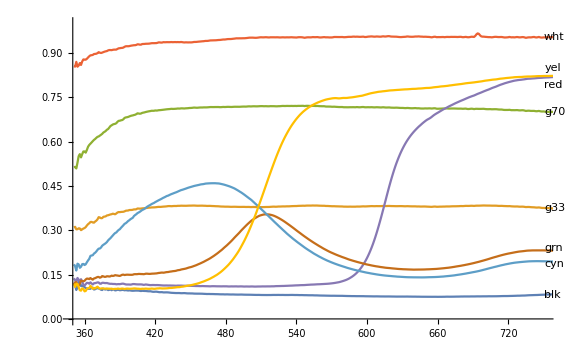

```mathematica
ListLinePlot[
Labeled[#⟦"reflectance"⟧,#⟦"Label"⟧]&/@Flatten[Values[calTargetSpectraSelected]]
,PlotRange->{{350,750},{0,1}}
,ImageSize->Large
]
```

## Color Transformation Model Development

```mathematica
imageFileNames=FileNames["E*ECM*.png",{rawImagesDirectory}]; (* Descent down look raw files *)
```

```mathematica
calibrationImageFileName=First@Select[imageFileNames,StringMatchQ[__~~"ESF_0042_0670681098_128"~~__]](* ESF used for color calibration target *)
```

/Users/bswift/Downloads/mars2020/raw/esf/ESF_0042_0670681098_128ECM_N0031392EDLC00042_0020LUJ01.png

```mathematica
rawImageRGB=Import[calibrationImageFileName]
```

-Graphics-

```mathematica
csRawImage=ColorSeparate[rawImageRGB];
```

```mathematica
(* rawImage to uncorrected color image.
Currently only using 1 green of RGGB Bayer patern.
MM ImageDemosaic functio not documented enough to be useful.
*)
debayerPlane1=ImageTake[csRawImage⟦1⟧,{1,-1,2},{1,-1,2}]; (* Red *)
debayerPlane2=ImageTake[csRawImage⟦3⟧,{2,-1,2},{2,-1,2}]; (* Blue *)
debayerPlane3=ImageTake[csRawImage⟦2⟧,{2,-1,2},{1,-1,2}]; (* Green *)
debayerPlane4=ImageTake[csRawImage⟦2⟧,{1,-1,2},{2,-1,2}];(* Green *)
```

```mathematica
debayerPlanes={debayerPlane1,debayerPlane2,debayerPlane3,debayerPlane4};
```

```mathematica
debayerPlanesImage=ColorCombine[{debayerPlane1,0.5 (debayerPlane3 +debayerPlane4),debayerPlane2},"RGB"]
```

-Graphics-

### Color Targets

```mathematica
darkToLightRGCY={{548.361328125,575.390625},{545.005859375,597.822265625},{525.638671875,610.7890625},{503.837890625,607.126953125},{535.658203125,555.798828125},{489.93359375,588.14453125},{512.962890625,552.681640625},{493.94140625,565.11328125}};(* Primary target samples ordered dark to light then Red Green Cyan Yellow. Note two lightest samples experiencing cllipping of Red and Green.  "ESF_0042_0670681098_128ECM_N0031392EDLC00042_0020LUJ01.png"*)
```

```mathematica
discsRoughCenterPane1=darkToLightRGCY
```

{{548.361,575.391},{545.006,597.822},{525.639,610.789},{503.838,607.127},{535.658,555.799},{489.934,588.145},{512.963,552.682},{493.941,565.113}}

```mathematica
cutOut[image_Image,{x_,y_},{columns_,rows_}]:=ImageTake[image
,(ImageDimensions[image]⟦2⟧-Floor[y])+{-1,1}Ceiling[(rows-1)/2]
,Floor[x]+{-1,1}Ceiling[(columns-1)/2]
]
```

```mathematica
Map[cutOut[debayerPlane1,#+{1,0},{1,1}+15]&,discsRoughCenterPane1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
cutoutsPlaneChip=Outer[cutOut[#1,#2+{1,0}+{1,1},{1,1}+2(* up to 8 for vertical chips avoiding shadow *)(* up to 11 for horizontal chips *)
]&,debayerPlanes,discsRoughCenterPane1,1] (* from each color plane extract calibration chip image around RoughCenter points *)
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Map[Times@@ImageDimensions[#]&,cutoutsPlaneChip,{2}]
```

{{9,9,9,9,9,9,9,9},{9,9,9,9,9,9,9,9},{9,9,9,9,9,9,9,9},{9,9,9,9,9,9,9,9}}

```mathematica
darkToLightPlanes=Map[TrimmedMean[#, 2/Times@@ImageDimensions[#]]&,cutoutsPlaneChip,{2}] (* RBGG *)
```

{{0.130196,0.527843,0.89098,0.996078,0.497255,0.254118,0.211765,0.821961},{0.0745098,0.306667,0.524706,0.586667,0.0964706,0.178824,0.261176,0.189804},{0.17098,0.727059,0.996078,0.996078,0.298824,0.46902,0.457255,0.936471},{0.176471,0.72549,0.996078,0.996078,0.300392,0.473725,0.442353,0.905098}}

```mathematica
Map[(ImageData[255 #]//MatrixForm)&,cutoutsPlaneChip,{2}]
```

{{(33. | 36. | 38.
33. | 32. | 34.
32. | 33. | 33.),(132. | 136. | 139.
135. | 133. | 135.
136. | 134. | 133.),(226. | 228. | 224.
227. | 228. | 227.
225. | 230. | 229.),(254. | 254. | 254.
254. | 254. | 254.
254. | 254. | 254.),(126. | 127. | 124.
127. | 127. | 127.
127. | 129. | 120.),(64. | 66. | 64.
66. | 65. | 65.
63. | 66. | 64.),(55. | 52. | 54.
54. | 53. | 55.
53. | 54. | 55.),(197. | 202. | 189.
214. | 217. | 207.
214. | 220. | 211.)},{(18. | 19. | 19.
19. | 19. | 19.
18. | 19. | 19.),(79. | 79. | 78.
78. | 80. | 77.
79. | 77. | 77.),(133. | 138. | 134.
131. | 136. | 132.
137. | 134. | 132.),(150. | 147. | 149.
150. | 148. | 149.
152. | 154. | 150.),(24. | 24. | 25.
24. | 25. | 26.
23. | 25. | 25.),(45. | 46. | 47.
46. | 45. | 45.
46. | 46. | 43.),(66. | 66. | 63.
67. | 68. | 67.
68. | 67. | 65.),(48. | 49. | 47.
51. | 51. | 46.
47. | 51. | 46.)},{(43. | 43. | 44.
45. | 44. | 42.
44. | 44. | 41.),(187. | 183. | 188.
184. | 180. | 185.
188. | 185. | 186.),(254. | 254. | 254.
254. | 254. | 254.
254. | 254. | 254.),(254. | 254. | 254.
254. | 254. | 254.
254. | 254. | 254.),(78. | 76. | 77.
74. | 76. | 77.
73. | 77. | 75.),(120. | 123. | 119.
120. | 118. | 119.
121. | 120. | 118.),(117. | 115. | 115.
114. | 118. | 114.
119. | 118. | 118.),(236. | 240. | 229.
240. | 240. | 234.
242. | 240. | 238.)},{(46. | 46. | 50.
43. | 44. | 47.
43. | 44. | 45.),(186. | 189. | 187.
179. | 183. | 187.
186. | 183. | 177.),(254. | 254. | 254.
254. | 254. | 254.
254. | 254. | 254.),(254. | 254. | 254.
254. | 254. | 254.
254. | 254. | 254.),(76. | 76. | 78.
77. | 79. | 74.
78. | 76. | 76.),(121. | 121. | 120.
121. | 122. | 121.
124. | 120. | 119.),(114. | 115. | 109.
114. | 114. | 112.
114. | 110. | 110.),(227. | 227. | 213.
242. | 233. | 219.
243. | 240. | 227.)}}

### Multi-parameter Optimization

```mathematica
calTargetSpectraSelected⟦All,1,"Label"⟧
```

{blk,g33,g70,wht,red,grn,cyn,yel}

```mathematica
calTargetRAWRGB=RGBColor@@@Transpose[{darkToLightPlanes⟦1⟧,Mean[darkToLightPlanes⟦{3,4}⟧],darkToLightPlanes⟦2⟧}] (* darkToLightRGCY *)
```

{RGBColor[0.13019607843137254, 0.17372549019607844, 0.07450980392156863],RGBColor[0.527843137254902, 0.7262745098039216, 0.3066666666666667],RGBColor[0.8909803921568628, 0.996078431372549, 0.5247058823529411],RGBColor[0.996078431372549, 0.996078431372549, 0.5866666666666667],RGBColor[0.4972549019607843, 0.2996078431372549, 0.09647058823529411],RGBColor[0.2541176470588235, 0.4713725490196079, 0.17882352941176471],RGBColor[0.21176470588235294, 0.4498039215686275, 0.2611764705882353],RGBColor[0.8219607843137254, 0.9207843137254902, 0.18980392156862744]}

```mathematica
calTargetSpectraDiscrete=Map[{λXYZCMF⟦1⟧,#⟦1,"reflectanceIF"⟧[λXYZCMF⟦1⟧]}&
,calTargetSpectraSelected]; (* resample calibration target spectra to color matching function wavelengths *)
```

```mathematica
calTargetRAWRGBWeights={1,1,.01,.01,.5,.5,.5,.4}(* darkToLightRGCY *)
```

{1,1,0.01,0.01,0.5,0.5,0.5,0.4}

```mathematica
(* modelW10 - IDT and black-body illuminant temp. *)
(* IDT model from DRAFT P-2013-001:Recommended Procedures for the Creation and Use of Digital Camera System Input Device Transforms (IDTs) http://j.mp/P-2013-001 https://www.oscars.org/science-technology/aces/aces-documentation *)

modelW10=.;
modelW10[
β1_?NumericQ,β2_,β3_,β4_,β5_,β6_ (* IDT *)
,bands_
,weights_ (* for each sample *)
]:=
Block[
{illuminantDiscrete=blackBodyDiscrete[bands⟦1⟧],
optimizedIlluminantXYZ
},
(*optimizedIlluminantXYZ=(λXYZCMF⟦2;;4⟧.illuminantDiscrete⟦2⟧)//#/#⟦2⟧&;*)
RootMeanSquare[
WeightedData[
MapThread[
ColorDistance[#1,#2,DistanceFunction->"CIE2000" ]&
,{(XYZColor[
({{β1,β2,1-β1-β2}
,{β3,β4,1-β3-β4}
,{β5,β6,1-β5-β6}
}.{ #⟦1⟧
, #⟦2⟧
, #⟦3⟧
})⟦1;;3⟧
]&/@calTargetRAWRGB)
,(XYZColor[.01 #]&/@( Map[reflectanceToXYZDiscrete[#,illuminantDiscrete]&,calTargetSpectraDiscrete]))}],
weights]
]
]
```

```mathematica
(* modelW11 - IDT assuming D65 illuminant. *)
modelW11=.;
modelW11[
β1_?NumericQ,β2_,β3_,β4_,β5_,β6_ (* IDT *)
,weights_ (* for each sample *)
]:=
Block[
{illuminantDiscrete=illuminantD65Discrete,
optimizedIlluminantXYZ
},
(*optimizedIlluminantXYZ=(λXYZCMF⟦2;;4⟧.illuminantDiscrete⟦2⟧)//#/#⟦2⟧&;*)
RootMeanSquare[
WeightedData[
MapThread[
ColorDistance[#1,#2,DistanceFunction->"CIE2000" ]&
,{(XYZColor[
({{β1,β2,1-β1-β2}
,{β3,β4,1-β3-β4}
,{β5,β6,1-β5-β6}
}.{ #⟦1⟧
, #⟦2⟧
, #⟦3⟧
})⟦1;;3⟧
]&/@calTargetRAWRGB)
,(XYZColor[.01 #]&/@( Map[reflectanceToXYZDiscrete[#,illuminantDiscrete]&,calTargetSpectraDiscrete]))}],
weights]
]
]
```

```mathematica
modelW10[1,0
,0,1
,0,0
,{5777.} (* Solar AM0 *)
,calTargetRAWRGBWeights
]
```

0.298783

```mathematica
modelW11[1,0
,0,1
,0,0
,calTargetRAWRGBWeights
]
```

0.308398

```mathematica
AbsoluteTiming[
optResultsM11=NMinimize[
{
modelW11[
β1,β2,β3,β4,β5,β6
,calTargetRAWRGBWeights]
}
,{β1,β2,β3,β4,β5,β6
}
,Method->{"RandomSearch","SearchPoints"-> 30} 
]
]
```

{16.3833,{0.113158,{β1→0.415247,β2→-0.0741459,β3→0.216901,β4→0.106853,β5→-0.0462251,β6→0.167533}}}

```mathematica
AbsoluteTiming[
optResultsM10=NMinimize[
{
modelW10[
β1,β2,β3,β4,β5,β6
,{b1}
,calTargetRAWRGBWeights]
,1000<b1<10000
}
,{β1,β2,β3,β4,β5,β6
,b1
}
,Method->{"RandomSearch","SearchPoints"-> 30} 
]
]
```

{55.1468,{0.0539836,{β1→0.636906,β2→-0.0370224,β3→0.337894,β4→0.0735785,β5→0.123875,β6→-0.351916,b1→3086.25}}}

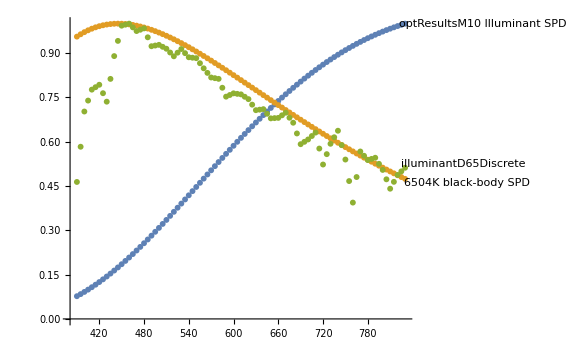

```mathematica
ListPlot[{Labeled[blackBodyDiscrete[b1/.optResultsM10⟦2⟧]ᵀ,"optResultsM10 Illuminant SPD"]
,Labeled[blackBodyDiscrete[6504.]ᵀ,"6504K black-body SPD"]
,Labeled[({#⟦1⟧,#⟦2⟧/Max[#⟦2⟧]}&@illuminantD65Discrete)ᵀ,"illuminantD65Discrete"]}
,ImageSize->Large]
```

### Color De-saturate clipping pixels

```mathematica
(* Blue channel on IMX264 is less sensitive than Red and Green, so doesn't clip until much higher brightness, so can be used to modulate final image saturation in areas where Red or Green raw data is clipping *)
```

```mathematica
saturatedMaskPlanes=(Binarize[#,253.99/255]&/@debayerPlanes);
allSaturatedMask=ImageMultiply@@saturatedMaskPlanes;
noneSaturatedMask=ImageMultiply@@(1-saturatedMaskPlanes);
someSaturatedMask=(1-noneSaturatedMask)(1-allSaturatedMask);
```

```mathematica
x=.
```

```mathematica
deSaturateFactorLM=LinearModelFit[{{.5,1},{.98,0}},x,x]
```

FittedModel[2.04167-2.08333 x]

```mathematica
deSaturateFactorLM=LinearModelFit[{{.6,.25},{.98,0}},x,x]
```

FittedModel[0.644737-0.657895 x]

```mathematica
disableDesaturationMask=(1-Binarize[debayerPlanes⟦2⟧,100./254])+noneSaturatedMask (* Blue < 100 or none saturated
So only getting applied when blue getting large. Don't want capton tape getting desaturated. *)(* + to "or" masks together *)
```

-Graphics-

```mathematica
deSaturateFactorImage=ImageClip[deSaturateFactorLM[debayerPlanes⟦2⟧]+2disableDesaturationMask] (* +2x to "or" disableDesaturationMask on top of blue channel based desaturation *)(* result, black areas will be completely desaturated, grey areas will be somewhat desaturated, white areas will not be left unchanged *)
```

-Graphics-

### Transform Raw Image via model

```mathematica
rawToXYZIDT=({{β1,β2,1-β1-β2}
,{β3,β4,1-β3-β4}
,{β5,β6,1-β5-β6}
}/.optResultsM10⟦2⟧)
```

{{0.636906,-0.0370224,0.400116},{0.337894,0.0735785,0.588528},{0.123875,-0.351916,1.22804}}

```mathematica
optimizedIlluminantXYZ=blackBodyXYZ[b1]/.optResultsM10⟦2⟧
```

{1.08065,1,0.398841}

```mathematica
XYZColor[optimizedIlluminantXYZ]
```

XYZColor[{1.0806453069739346, 1, 0.39884089257738076}]

```mathematica
(* scaled rawRGB -> XYZ -> chromatic adaption XYZ -> okLab *)
intermediatOkLabPlanes=xyzToOkLab[
xyzAdaptedPlanes=
(adaptMat[catMatBS(*catMatBradford*),optimizedIlluminantXYZ,d65XYZBL].(xyzFromRawPlanes=rawToXYZIDT.( .91 ColorSeparate[debayerPlanesImage])
)
)
]; (* Model 10,  .91 brings max area white in sRGB to 254 *)
```

```mathematica
(* selective desaturation by scaling of "a" and "b" in okLab color-space, transform okLab back to XYZ and then XYZ to sRGB-linear *)
sRGBLinearDesatImage=ColorCombine[sRGBLinearDesatPlanes=Inverse[linearRGBtoXYZMat[srgbPrimaries,d65XYZBL]].okLabToXYZ[{1,(*1+0*)deSaturateFactorImage,(*1+0*)deSaturateFactorImage}intermediatOkLabPlanes]
,"RGB"];
```

```mathematica
gamutReducedImage=linear2srgbImageReal[ImageClip[sRGBLinearDesatImage]]
```

-Graphics-

## Bulk Processing

### Process multiple RAW ECAM images

```mathematica
(* transform raw image to video frame using model10 and model11 *)
processECAM2[image_Image]:=Block[{
rawImageRGB
,csRawImage
,debayerPlane1
,debayerPlane2
,debayerPlane3
,debayerPlane4
,debayerPlanes
,debayerPlanesImage
,saturatedMaskPlanes
,allSaturatedMask
,noneSaturatedMask
,someSaturatedMask
,anySaturatedMask

,disableDesaturationMask
,deSaturateFactorImage

,rawToXYZIDT
,optimizedIlluminantXYZ
,intermediatOkLabPlanes
,sRGBLinearDesatImage
,gamutReducedImageM10
,gamutReducedImageM11

,finalImage
}
,
rawImageRGB=image;
csRawImage=ColorSeparate[rawImageRGB];
debayerPlane1=ImageTake[csRawImage⟦1⟧,{1,-1,2},{1,-1,2}]; (* Red *)
debayerPlane2=ImageTake[csRawImage⟦3⟧,{2,-1,2},{2,-1,2}]; (* Blue *)
debayerPlane3=ImageTake[csRawImage⟦2⟧,{2,-1,2},{1,-1,2}]; (* Green *)
debayerPlane4=ImageTake[csRawImage⟦2⟧,{1,-1,2},{2,-1,2}];(* Green *)
debayerPlanes={debayerPlane1,debayerPlane2,debayerPlane3,debayerPlane4};
debayerPlanesImage=ColorCombine[{debayerPlane1,0.5 (debayerPlane3 +debayerPlane4),debayerPlane2},"RGB"];
saturatedMaskPlanes=(Binarize[#,253.99/255]&/@debayerPlanes);
allSaturatedMask=ImageMultiply@@saturatedMaskPlanes;
noneSaturatedMask=ImageMultiply@@(1-saturatedMaskPlanes);
someSaturatedMask=(1-noneSaturatedMask)(1-allSaturatedMask);(* some but not all saturated *)
anySaturatedMask=(1-noneSaturatedMask); 
disableDesaturationMask=(1-Binarize[debayerPlanes⟦2⟧,100./254])+noneSaturatedMask;
deSaturateFactorImage=ImageClip[deSaturateFactorLM[debayerPlanes⟦2⟧]+2disableDesaturationMask];

(* Model 10 *)
rawToXYZIDT=({{β1,β2,1-β1-β2}
,{β3,β4,1-β3-β4}
,{β5,β6,1-β5-β6}
}/.optResultsM10⟦2⟧);
optimizedIlluminantXYZ=blackBodyXYZ[b1]/.optResultsM10⟦2⟧;
intermediatOkLabPlanes=xyzToOkLab[
(adaptMat[catMatBS(*catMatBradford*),optimizedIlluminantXYZ,d65XYZBL].(rawToXYZIDT.( .91 ColorSeparate[debayerPlanesImage])
)
)
]; (* Model 10,  .91 brings max area white in sRGB to 254 *)
sRGBLinearDesatImage=ColorCombine[Inverse[linearRGBtoXYZMat[srgbPrimaries,d65XYZBL]].okLabToXYZ[{1,(*1+0*)deSaturateFactorImage,(*1+0*)deSaturateFactorImage}intermediatOkLabPlanes]
,"RGB"];
gamutReducedImageM10=linear2srgbImageReal[ImageClip[sRGBLinearDesatImage]];

(* Model 11 *)
rawToXYZIDT=({{β1,β2,1-β1-β2}
,{β3,β4,1-β3-β4}
,{β5,β6,1-β5-β6}
}/.optResultsM11⟦2⟧);
intermediatOkLabPlanes=xyzToOkLab[
rawToXYZIDT.( .98 ColorSeparate[debayerPlanesImage])
]; (* Model 11 , .98 brings max area white in sRGB to 254 *)
sRGBLinearDesatImage=ColorCombine[Inverse[linearRGBtoXYZMat[srgbPrimaries,d65XYZBL]].okLabToXYZ[{1,(*1+0*)deSaturateFactorImage,(*1+0*)deSaturateFactorImage}intermediatOkLabPlanes]
,"RGB"];
gamutReducedImageM11=linear2srgbImageReal[ImageClip[sRGBLinearDesatImage]];

finalImage=ImageAssemble[{{gamutReducedImageM10,gamutReducedImageM11 }}];
finalImage
(*ImageRotate[gamutReducedImageM10,180°]*)(* 180° rotation to match JPL video *)
]
```

```mathematica
processedDirectory=StringReplace[DirectoryName[imageFileNames⟦1⟧],"/raw/"-> "/frames/"]
```

/Users/bswift/Downloads/mars2020/frames/esf/

```mathematica
CreateDirectory[processedDirectory]
```

/Users/bswift/Downloads/mars2020/frames/esf/

```mathematica
DirectoryQ[processedDirectory]
```

True

```mathematica
framePrefix=FileNameTake[processedDirectory]<>"_" (* set to give Compressor a prefix for movie filename *)
```

esf_

```mathematica
imageFilenameSelector=6(*6 esf *);;-1 (* Skip first 6 raw images. These were processed differently at JPL. *)
```

6;;-1

```mathematica
AbsoluteTiming[
Parallelize[
processResults=MapIndexed[
Export[
FileNameJoin[{processedDirectory,framePrefix<>ToString[50000+First[#2]]<>".png"(*"_"<>FileNameTake[#1]*)}] (* 50000 to get fixed lenght frame number and have range to add sequences before *)
,processECAM2[Import[#]]]&
,imageFileNames⟦imageFilenameSelector⟧
];
]
]
```

{62.8013,Null}

```mathematica
processResults//Length
```

72